# The metrology of quantum coherence

Dr Jesús Rubio
University of Surrey
j.rubiojimenez@surrey.ac.uk
ORCID iD: 0000-0002-8193-8273

Created: May 2024
Last update: July 2025

## Weight estimation

### Prior information

Prior probability:

```mathematica
Clear[a,θmin,θmax,pweight]
θmin[a_]=1-a;
θmax[a_]=a;
pweight[θ_,a_]:=1/(θ(1-θ) NIntegrate[1/(x(1-x)),{x,θmin[a],θmax[a]}])//Quiet
```

Symmetry function:

```mathematica
Clear[fweight]
fweight[θ_]=2ArcTanh[2θ-1];
```

Prior uncertainty:

```mathematica
Clear[ϵpriorWeight]
ϵpriorWeight[a_]:=NIntegrate[pweight[x,a] fweight[x]^2,{x,θmin[a],θmax[a]}]-NIntegrate[pweight[x,a]fweight[x],{x,θmin[a],θmax[a]}]^2//Quiet
```

### Probe state

```mathematica
Clear[ψ,ρqubit,ρ]
ψ[θ_]:={Sqrt[θ],Sqrt[1-θ]}
ρqubit[θ_]:=KroneckerProduct[Transpose[ψ[θ]],ψ[θ]]
ρ[θ_,λ_]:=(1-λ)ρqubit[θ]+λ{{1,0},{0,1}}/2
```

### ρ_0, ρ_1 and S operators

```mathematica
Clear[ρ0weight ,ρ1weight,Sweight]
ρ0weight[a_,λ_]:=NIntegrate[pweight[x,a] ρ[x,λ],{x,θmin[a],θmax[a]}];
ρ1weight[a_,λ_]:=NIntegrate[pweight[x,a] ρ[x,λ]fweight[x],{x,θmin[a],θmax[a]}]//Quiet;
Sweight[a_,λ_]:=LyapunovSolve[ρ0weight[a,λ],ρ0weight[a,λ],2ρ1weight[a,λ]];
```

### Relative precision gain on average

```mathematica
Clear[εweight]
εweight[a_,λ_]:=(Tr[ρ1weight [a,λ].Sweight[a,λ]]-NIntegrate[pweight[x,a]fweight[x],{x,θmin[a],θmax[a]}]^2)/ϵpriorWeight[a]//Quiet
```

## Geometric approach

### Symmetry function

```mathematica
Clear[fmetric]
fmetric[θ_]=2ArcTan[Sqrt[θ/(1-θ)]]
```

2 ArcTan[√(θ/(1-θ))]

### Jeffreys’s general rule

```mathematica
Clear[aux,pmetric]
aux[θ_]=D[fmetric[θ],θ];
pmetric[θ_,a_]:=aux[θ]/(fmetric[θmax[a]]-fmetric[θmin[a]])
```

### ρ_0, ρ_1 and S operators

```mathematica
Clear[ρ0metric, ρ1metric,Smetric]
ρ0metric[a_,λ_]:=NIntegrate[pmetric[x,a] ρ[x,λ],{x,θmin[a],θmax[a]}];
ρ1metric[a_,λ_]:=NIntegrate[pmetric[x,a] ρ[x,λ]fmetric[x],{x,θmin[a],θmax[a]}];
Smetric[a_,λ_]:=LyapunovSolve[ρ0metric[a,λ],ρ0metric[a,λ],2ρ1metric[a,λ]];
```

### Prior uncertainty

```mathematica
Clear[ϵpriorMetric]
ϵpriorMetric[a_]:=NIntegrate[pmetric[x,a] fmetric[x]^2,{x,θmin[a],θmax[a]}]-NIntegrate[pmetric[x,a]fmetric[x],{x,θmin[a],θmax[a]}]^2
```

### Relative precision gain on average

```mathematica
Clear[εmetric]
εmetric[a_,λ_]:=(Tr[ρ1metric[a,λ].Smetric[a,λ]]-NIntegrate[pmetric[x,a]fmetric[x],{x,θmin[a],θmax[a]}]^2)/ϵpriorMetric[a]//Quiet
```

## Plots

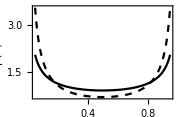

```mathematica
aplot=0.95;
insetCoherence=Plot[{pmetric[x,aplot],pweight[x,aplot]},{x,1-aplot,aplot},FrameStyle->Directive["Times",13,Black],Frame->True,PlotStyle->{{Black},{Dashed,Black}},FrameLabel->{"θ","p(θ)"},AspectRatio->0.65,PlotRange->{All,All},ImageSize->Small]
```

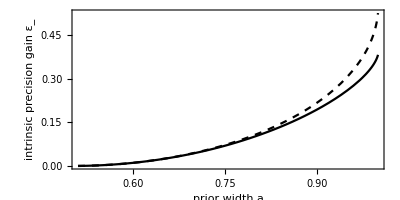

```mathematica
Plot[{εmetric[a,0.1],εweight[a,0.1]},{a,0.51,0.999},FrameStyle->Directive["Times",13,Black],Frame->True,PlotStyle->{{Black},{Dashed,Black}},FrameLabel->{"prior width a","intrinsic precision gain ε_"},AspectRatio->0.50,PlotRange->{All,All},Epilog->{Inset[insetCoherence,ImageScaled[{0.385,0.645}]]}]
```